# Leads connected to 1 - 10 and 41 to 50

```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->t]
```

```mathematica
T1[t_]:= t*IdentityMatrix[10]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["/home/shardul/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.4,0.01]}]
```

```mathematica
leads[50][[1]]
```

{{0.-0.848777 ⅈ,-0.499958+0. ⅈ,0.+0.169765 ⅈ,0.0000168958+0. ⅈ,0.+0.0242514 ⅈ,0.0000107923+0. ⅈ,0.+0.00808295 ⅈ,7.92214×10^-6+0. ⅈ,35,4.29716×10^-7+0. ⅈ,0.+0.0000144261 ⅈ,3.04572×10^-7+0. ⅈ,0.+9.37419×10^-6 ⅈ,1.81811×10^-7+0. ⅈ,0.+4.616×10^-6 ⅈ,6.04496×10^-8+0. ⅈ},{1},47,{1}}
 |  |  |  |

```mathematica
Clear[LEFT]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]](*Module[{J=Inverse[β[ω,0.0001,1,0,m]],A:=Inverse[β[ω,0.0001,1,0,m]],T:=T1[1]},Do[J=Inverse[IdentityMatrix[m]-A.T.J.T].A,50000];J=J]*)
```

```mathematica
device1[0]
```

{{0.-0.464237 ⅈ,0.374995+0. ⅈ,0.+0.27193 ⅈ,-0.187485+0. ⅈ,0.-0.130725 ⅈ,0.0937401+0. ⅈ,0.+0.0670162 ⅈ,-0.0468664+0. ⅈ,34,0.+2.4513×10^-6 ⅈ,-1.32282×10^-7+0. ⅈ,0.+1.46725×10^-6 ⅈ,1.25944×10^-7+0. ⅈ,0.+1.09363×10^-6 ⅈ,-3.00341×10^-8+0. ⅈ,0.+4.85747×10^-7 ⅈ,4.0205×10^-8+0. ⅈ},48,{1}}
 |  |  |  |

```mathematica
fffff[y_,z_]:= Table[{x,y},{x,1,z}]
```

```mathematica
sssss[z_]:=Module[{J=fffff[1,z]},Do[J=Join[fffff[y,z],J],{y,2,z}];J=J]
```

```mathematica
sssss[50]
```

{{1,50},{2,50},{3,50},{4,50},{5,50},{6,50},{7,50},{8,50},{9,50},{10,50},{11,50},{12,50},{13,50},{14,50},{15,50},{16,50},{17,50},{18,50},{19,50},{20,50},{21,50},{22,50},{23,50},{24,50},{25,50},{26,50},{27,50},{28,50},{29,50},{30,50},{31,50},{32,50},{33,50},2434,{18,1},{19,1},{20,1},{21,1},{22,1},{23,1},{24,1},{25,1},{26,1},{27,1},{28,1},{29,1},{30,1},{31,1},{32,1},{33,1},{34,1},{35,1},{36,1},{37,1},{38,1},{39,1},{40,1},{41,1},{42,1},{43,1},{44,1},{45,1},{46,1},{47,1},{48,1},{49,1},{50,1}}
 |  |  |  |

```mathematica
Clear[a]
```

```mathematica
Clear[dist]
```

```mathematica
dist[concentration_]:=dist[concentration]=Table[SortBy[RandomSample[sssss[50],concentration],First],1000]
```

```mathematica
dist[50][[1]]
```

{{3,31},{4,38},{5,28},{6,48},{6,50},{7,15},{7,23},{7,36},{9,4},{10,4},{10,12},{10,30},{10,45},{11,26},{15,22},{15,44},{18,26},{19,4},{21,6},{21,17},{23,50},{24,24},{25,10},{25,31},{25,48},{26,15},{27,25},{27,38},{30,33},{31,18},{32,11},{36,22},{36,32},{37,15},{40,7},{40,25},{41,20},{41,25},{41,29},{42,46},{44,31},{46,16},{46,32},{47,18},{48,12},{48,21},{49,1},{49,15},{49,17},{50,12}}

```mathematica
Clear[f]
```

```mathematica
f[ω_,δ_,t_,ϵ_,ϵ1_,unitcell_,concentration_,number_]:=Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,1,50}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;50,1;;50]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=50},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,50].LEFT[ω,50].T[1,50]].g[ω,0.0001,1,0]]
```

```mathematica
CA[ω_,δ_,t_,ϵ_,ϵ1_,concentration_,number_]:= Module[{sizeoflead=50},
recurs=Module[{J1= device1[ω]},
Do[
J1=Inverse[IdentityMatrix[50]-Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]].T[1,50].J1.T[1,50]].Inverse[Module[{J=β[ω,δ,t,ϵ,50]},Do[J=Module[{m=unitcell},If[dist[concentration][[number]][[loc1,1]]==m,ReplacePart[J,{{dist[concentration][[number]][[loc1,2]],dist[concentration][[number]][[loc1,2]]}}->ω+ⅈ*δ-ϵ1],J]],{loc1,concentration}];J]],{unitcell,50}];J1=J1];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
transmission=Table[{conc,Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/complete/leads_1_10_and_41_50/full_device/ϵ1_conc_"<>ToString[conc]<>"_.dat"]},{conc,10,140,10}]
```

{{10,{{0.,8.20345},{0.01,7.19567},{0.02,6.44567},{0.03,5.6569},{0.04,5.4354},{0.05,4.52895},{0.06,4.45416},{0.07,4.43167},{0.08,5.01419},284,{2.93,1.15746},{2.94,1.67728},{2.95,1.43777},{2.96,1.51666},{2.97,1.44988},{2.98,1.24043},{2.99,1.61067},{3.,1.74349}}},12,{140,{1}}}
 |  |  |  |

```mathematica
Dimensions[%30]
```

{14,301,2}

```mathematica
input= Monitor[Table[Table[{ω,Print[ω];CA[ω,0.0001,1,0,0,50,num]},{ω,Range[0,2,0.01]}],{num,2}],num]
```

{{{0.,46.4971},{0.01,25.029},{0.02,19.8513},{0.03,17.2368},{0.04,16.6216},{0.05,16.1529},{0.06,18.5347},{0.07,19.8145},{0.08,22.3564},{0.09,24.7816},{0.1,24.7417},{0.11,23.0035},{0.12,22.0788},{0.13,20.7187},{0.14,18.901},{0.15,18.009},{0.16,17.9309},{0.17,18.4767},{0.18,19.5096},{0.19,20.1508},{0.2,21.3192},{0.21,21.3316},{0.22,21.8572},{0.23,20.7473},{0.24,21.0528},{0.25,18.678},{0.26,19.1756},{0.27,18.1044},{0.28,18.1575},{0.29,18.2168},{0.3,18.5521},{0.31,19.7841},{0.32,19.1582},{0.33,20.6074},{0.34,20.1225},{0.35,19.9459},{0.36,18.5323},{0.37,18.9503},{0.38,18.0345},{0.39,17.8101},{0.4,17.6202},{0.41,17.2798},{0.42,17.8323},{0.43,18.6363},{0.44,17.6829},{0.45,18.0957},{0.46,19.135},{0.47,18.37},{0.48,18.0544},{0.49,17.2843},{0.5,17.3506},{0.51,16.7323},{0.52,16.8978},{0.53,16.3803},{0.54,16.1716},{0.55,16.881},{0.56,17.6808},{0.57,16.7944},{0.58,16.585},{0.59,16.9127},{0.6,16.8521},{0.61,16.5541},{0.62,15.4018},{0.63,15.4858},{0.64,15.8175},{0.65,15.0765},{0.66,16.6643},{0.67,15.2039},{0.68,15.0793},{0.69,15.4674},{0.7,17.0706},{0.71,16.3435},{0.72,15.3465},{0.73,15.0121},{0.74,14.6753},{0.75,14.0899},{0.76,15.5273},{0.77,13.6173},{0.78,14.2395},{0.79,13.2801},{0.8,14.8357},{0.81,14.8829},{0.82,15.0458},{0.83,14.4852},{0.84,14.4141},{0.85,14.3432},{0.86,14.7568},{0.87,13.7991},{0.88,13.3154},{0.89,11.8137},{0.9,11.7013},{0.91,11.8992},{0.92,12.4248},{0.93,12.8551},{0.94,13.8892},{0.95,13.1012},{0.96,13.633},{0.97,14.2338},{0.98,13.482},{0.99,12.0345},{1.,11.0677},{1.01,10.9757},{1.02,10.6421},{1.03,10.7626},{1.04,11.1207},{1.05,10.9678},{1.06,10.5273},{1.07,11.6582},{1.08,13.084},{1.09,13.1702},{1.1,11.9968},{1.11,10.5917},{1.12,9.99928},{1.13,9.84637},{1.14,9.38347},{1.15,9.91598},{1.16,10.3539},{1.17,9.0192},{1.18,9.19427},{1.19,9.99268},{1.2,11.4608},{1.21,11.7681},{1.22,10.2116},{1.23,9.05731},{1.24,9.04842},{1.25,8.16126},{1.26,8.26144},{1.27,8.96052},{1.28,8.43886},{1.29,7.93687},{1.3,8.75865},{1.31,8.77195},{1.32,10.6063},{1.33,9.88834},{1.34,8.06317},{1.35,7.36944},{1.36,7.49891},{1.37,6.81018},{1.38,7.13273},{1.39,8.16159},{1.4,7.34833},{1.41,7.04509},{1.42,7.73194},{1.43,7.59009},{1.44,8.18431},{1.45,6.60452},{1.46,6.13527},{1.47,6.00964},{1.48,6.30155},{1.49,5.76596},{1.5,6.08671},{1.51,7.11646},{1.52,6.37712},{1.53,6.17083},{1.54,6.11756},{1.55,5.242},{1.56,5.40323},{1.57,5.00895},{1.58,4.90139},{1.59,5.03889},{1.6,5.46051},{1.61,4.91818},{1.62,4.67714},{1.63,5.00213},{1.64,4.39632},{1.65,4.04439},{1.66,4.71192},{1.67,3.98418},{1.68,4.28219},{1.69,3.95096},{1.7,3.18501},{1.71,3.21308},{1.72,3.55058},{1.73,3.38124},{1.74,3.37161},{1.75,3.62435},{1.76,3.30163},{1.77,2.65911},{1.78,3.05842},{1.79,2.32732},{1.8,3.14062},{1.81,2.47832},{1.82,1.89066},{1.83,1.86644},{1.84,1.88971},{1.85,1.78576},{1.86,1.63939},{1.87,1.80181},{1.88,1.98422},{1.89,1.52807},{1.9,1.46667},{1.91,1.25732},{1.92,1.44121},{1.93,1.06897},{1.94,0.0190178},{1.95,0.00781469},{1.96,0.00789359},{1.97,0.00520249},{1.98,0.0052013},{1.99,0.00454664},{2.,0.00387461}},{{0.,46.4971},{0.01,25.029},{0.02,19.8513},{0.03,17.2368},{0.04,16.6216},{0.05,16.1529},{0.06,18.5347},{0.07,19.8145},{0.08,22.3564},{0.09,24.7816},{0.1,24.7417},{0.11,23.0035},{0.12,22.0788},{0.13,20.7187},{0.14,18.901},{0.15,18.009},{0.16,17.9309},{0.17,18.4767},{0.18,19.5096},{0.19,20.1508},{0.2,21.3192},{0.21,21.3316},{0.22,21.8572},{0.23,20.7473},{0.24,21.0528},{0.25,18.678},{0.26,19.1756},{0.27,18.1044},{0.28,18.1575},{0.29,18.2168},{0.3,18.5521},{0.31,19.7841},{0.32,19.1582},{0.33,20.6074},{0.34,20.1225},{0.35,19.9459},{0.36,18.5323},{0.37,18.9503},{0.38,18.0345},{0.39,17.8101},{0.4,17.6202},{0.41,17.2798},{0.42,17.8323},{0.43,18.6363},{0.44,17.6829},{0.45,18.0957},{0.46,19.135},{0.47,18.37},{0.48,18.0544},{0.49,17.2843},{0.5,17.3506},{0.51,16.7323},{0.52,16.8978},{0.53,16.3803},{0.54,16.1716},{0.55,16.881},{0.56,17.6808},{0.57,16.7944},{0.58,16.585},{0.59,16.9127},{0.6,16.8521},{0.61,16.5541},{0.62,15.4018},{0.63,15.4858},{0.64,15.8175},{0.65,15.0765},{0.66,16.6643},{0.67,15.2039},{0.68,15.0793},{0.69,15.4674},{0.7,17.0706},{0.71,16.3435},{0.72,15.3465},{0.73,15.0121},{0.74,14.6753},{0.75,14.0899},{0.76,15.5273},{0.77,13.6173},{0.78,14.2395},{0.79,13.2801},{0.8,14.8357},{0.81,14.8829},{0.82,15.0458},{0.83,14.4852},{0.84,14.4141},{0.85,14.3432},{0.86,14.7568},{0.87,13.7991},{0.88,13.3154},{0.89,11.8137},{0.9,11.7013},{0.91,11.8992},{0.92,12.4248},{0.93,12.8551},{0.94,13.8892},{0.95,13.1012},{0.96,13.633},{0.97,14.2338},{0.98,13.482},{0.99,12.0345},{1.,11.0677},{1.01,10.9757},{1.02,10.6421},{1.03,10.7626},{1.04,11.1207},{1.05,10.9678},{1.06,10.5273},{1.07,11.6582},{1.08,13.084},{1.09,13.1702},{1.1,11.9968},{1.11,10.5917},{1.12,9.99928},{1.13,9.84637},{1.14,9.38347},{1.15,9.91598},{1.16,10.3539},{1.17,9.0192},{1.18,9.19427},{1.19,9.99268},{1.2,11.4608},{1.21,11.7681},{1.22,10.2116},{1.23,9.05731},{1.24,9.04842},{1.25,8.16126},{1.26,8.26144},{1.27,8.96052},{1.28,8.43886},{1.29,7.93687},{1.3,8.75865},{1.31,8.77195},{1.32,10.6063},{1.33,9.88834},{1.34,8.06317},{1.35,7.36944},{1.36,7.49891},{1.37,6.81018},{1.38,7.13273},{1.39,8.16159},{1.4,7.34833},{1.41,7.04509},{1.42,7.73194},{1.43,7.59009},{1.44,8.18431},{1.45,6.60452},{1.46,6.13527},{1.47,6.00964},{1.48,6.30155},{1.49,5.76596},{1.5,6.08671},{1.51,7.11646},{1.52,6.37712},{1.53,6.17083},{1.54,6.11756},{1.55,5.242},{1.56,5.40323},{1.57,5.00895},{1.58,4.90139},{1.59,5.03889},{1.6,5.46051},{1.61,4.91818},{1.62,4.67714},{1.63,5.00213},{1.64,4.39632},{1.65,4.04439},{1.66,4.71192},{1.67,3.98418},{1.68,4.28219},{1.69,3.95096},{1.7,3.18501},{1.71,3.21308},{1.72,3.55058},{1.73,3.38124},{1.74,3.37161},{1.75,3.62435},{1.76,3.30163},{1.77,2.65911},{1.78,3.05842},{1.79,2.32732},{1.8,3.14062},{1.81,2.47832},{1.82,1.89066},{1.83,1.86644},{1.84,1.88971},{1.85,1.78576},{1.86,1.63939},{1.87,1.80181},{1.88,1.98422},{1.89,1.52807},{1.9,1.46667},{1.91,1.25732},{1.92,1.44121},{1.93,1.06897},{1.94,0.0190178},{1.95,0.00781469},{1.96,0.00789359},{1.97,0.00520249},{1.98,0.0052013},{1.99,0.00454664},{2.,0.00387461}}}

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],1*Module[{B1=Transpose[{m5[[1;;301]][[;;,1]],(m5[[1;;301,2]]-transmission[[con,2]][[1;;301,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y))(*+NIntegrate[Interpolation[B1][ω],{ω,-3,-0.5}]/((2.5)*100)*)]},{con,14}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

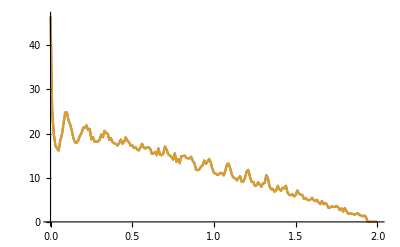

```mathematica
ListLinePlot[input]
```

```mathematica
Table[{n,misfit[01,2.5,n][[2]][[1]]},{n,50}]
```

{{1,50},{2,50},{3,60},{4,60},{5,40},{6,70},{7,60},{8,40},{9,50},{10,40},{11,90},{12,30},{13,30},{14,60},{15,60},{16,60},{17,30},{18,80},{19,70},{20,100},{21,50},{22,60},{23,60},{24,80},{25,50},{26,80},{27,50},{28,50},{29,50},{30,100},{31,40},{32,40},{33,30},{34,40},{35,40},{36,60},{37,50},{38,50},{39,60},{40,40},{41,40},{42,30},{43,40},{44,40},{45,50},{46,70},{47,30},{48,50},{49,40},{50,60}}

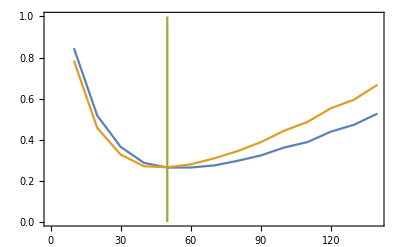

```mathematica
ListLinePlot[{misfit[1,2.5,1][[1]],misfit[1,2.5,2][[1]],Table[{50,x},{x,Range[0,1,0.01]}]},Frame->True]
```

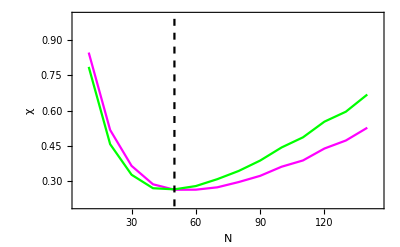

```mathematica
Show[ListLinePlot[{misfit[1,2.5,1][[1]],misfit[1,2.5,2][[1]],Table[{50,x},{x,Range[0,1.5,0.01]}]},PlotStyle->{Magenta,Green,Directive[Dashed,Black]},Frame->True],FrameLabel->{{HoldForm[χ],None},{HoldForm[N],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",15,GrayLevel[0]},PlotRange->{{5,145},{0.2,1}}]
```

```mathematica
Export["/home/shardulmukim/PhD/quantum_sudoq/hybrid.svg",%71]
```

/home/shardulmukim/PhD/quantum_sudoq/hybrid.svg